# Mathematica for Bioinformatics

## Chapter 8: Metabolomics Example

## Metabolomics Data

## Germ Free and Inoculated Mice Data

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
importGFMice=Import["GFMice.csv"];
```

### Processing Imported Data

```mathematica
importGFMice[[1;;4]]
```

{{Negative Mode,,,,,,,,,,,,,,,,,,,,,},{mzmed,GF1,GF2,GF3,Day5_BTBL_1,Day5_BTBL_2,Day5_BTBL_3,Day5_BTBL_4,Day10_BTBL_1,Day10_BTBL_2,Day10_BTBL_3,Day10_BTBL_4,Day15_BTBL_1,Day15_BTBL_2,Day15_BTBL_3,Day15_BTBL_4,Day20_BTBL_1,Day20_BTBL_2,Day20_BTBL_3,Day25_BTBL_1,Day25_BTBL_2,Day25_BTBL_3},{,0(GF),0(GF),0(GF),5,5,5,5,10,10,10,10,15,15,15,15,20,20,20,25,25,25},{269.125,4.77187×10^6,1.83739×10^6,2.69081×10^6,1.78109×10^6,1.95988×10^6,1.61111×10^6,1.84043×10^6,3.46027×10^6,7.17564×10^6,4.24283×10^6,5.18863×10^6,3.44216×10^6,5.37601×10^6,5.75372×10^6,5.62317×10^6,5.60079×10^6,4.82033×10^6,2.78184×10^6,2.68937×10^6,3.73472×10^6,5.98949×10^6}}

```mathematica
positiveModeLocation=Position[importGFMice,"Positive Mode"]
```

{{1559,1}}

```mathematica
Extract[importGFMice,positiveModeLocation]
```

{Positive Mode}

```mathematica
importGFMice[[1558;;1559+3]]
```

{{233.097,486634.,236327.,17058.,72046.,66187.,48386.7,100225.,86517.2,174761.,152207.,182583.,194218.,91068.7,185375.,195549.,182746.,173075.,125166.,149478.,156302.,110914.},{Positive Mode,,,,,,,,,,,,,,,,,,,,,},{mzmed,GF1,GF2,GF3,Day5_BTBL_1,Day5_BTBL_2,Day5_BTBL_3,Day5_BTBL_4,Day10_BTBL_1,Day10_BTBL_2,Day10_BTBL_3,Day10_BTBL_4,Day15_BTBL_1,Day15_BTBL_2,Day15_BTBL_3,Day15_BTBL_4,Day20_BTBL_1,Day20_BTBL_2,Day20_BTBL_3,Day25_BTBL_1,Day25_BTBL_2,Day25_BTBL_3},{,GF,GF,GF,5,5,5,5,10,10,10,10,15,15,15,15,20,20,20,25,25,25},{400.148,151323.,111751.,62803.1,37103.3,38007.8,40273.7,62485.1,45894.4,100245.,91827.7,103192.,110570.,64440.1,88330.9,79779.5,90142.1,77907.6,62669.8,51059.6,47668.2,61009.8}}

```mathematica
metabolitesGFRawData=Drop[importGFMice,{1559,1561}][[4;;,2;;]];
```

```mathematica
metabolitesGFAnnotations=importGFMice[[1561,2;;]]
```

{GF,GF,GF,5,5,5,5,10,10,10,10,15,15,15,15,20,20,20,25,25,25}

```mathematica
metabolitesGFFeatures=Drop[importGFMice,{1559,1561}][[4;;,1]];
```

```mathematica
metabolitesData=Drop[importGFMice,{1559,1561}][[4;;,2;;]];
```

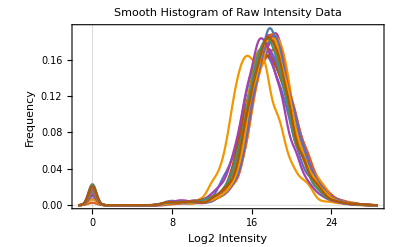

```mathematica
SmoothHistogram[ 
Log2[#+1]&@Transpose[metabolitesData],
PlotRange-> All,PlotTheme->"Scientific",
FrameLabel->{"Log2 Intensity","Frequency"},
PlotLabel->
"Smooth Histogram of Raw Intensity Data"]
```

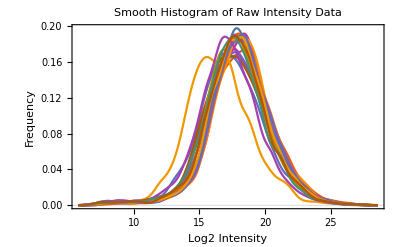

```mathematica
SmoothHistogram[ 
Log2[DeleteMissing[#]+1]&/@
(Transpose[metabolitesData]/. 
0|0.-> Missing[]),PlotRange-> All,
PlotTheme->"Scientific",
FrameLabel->{"Log2 Intensity","Frequency"},
PlotLabel->
"Smooth Histogram of Raw Intensity Data"]
```

```mathematica
<<MathIOmica`
```

MathIOmica (http://mathiomica.org), by [G. Mias Lab](http://georgemias.org).

```mathematica
standardizationLogs=
SeriesApplier[
StandardizeExtended[Log2[#],Mean,MeanDeviation]&,Transpose@metabolitesData/. 0|0.-> Missing[]];
```

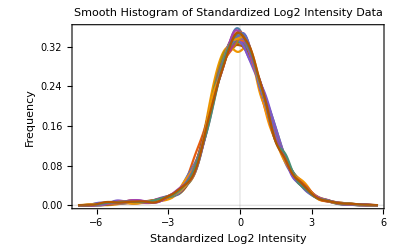

```mathematica
SmoothHistogram[ 
DeleteMissing[#]&/@standardizationLogs,
PlotRange-> All,PlotTheme->"Scientific",
FrameLabel->{"Standardized Log2 Intensity",
"Frequency"},
PlotLabel->
"Smooth Histogram of Standardized Log2 Intensity Data"]
```

```mathematica
?ApplyBoxCoxTransform
```

ApplyBoxCoxTransform[data] for a given data set, computes the Box-Cox transformation at the maximum likelihood λ parameter.

```mathematica
boxCoxTransformedMetaboliteData=ApplyBoxCoxTransform[#]&/@Transpose[metabolitesData/. 0|0.-> Missing[]];
```

Calculated Box-Cox parameter λ̂ = -0.00130934

Calculated Box-Cox parameter λ̂ = 0.0126927

Calculated Box-Cox parameter λ̂ = -0.0109138

Calculated Box-Cox parameter λ̂ = 0.036568

Calculated Box-Cox parameter λ̂ = 0.0434655

Calculated Box-Cox parameter λ̂ = 0.0334664

Calculated Box-Cox parameter λ̂ = 0.0447434

Calculated Box-Cox parameter λ̂ = 0.0312509

Calculated Box-Cox parameter λ̂ = 0.0343907

Calculated Box-Cox parameter λ̂ = 0.0352078

Calculated Box-Cox parameter λ̂ = 0.0268172

Calculated Box-Cox parameter λ̂ = 0.0288383

Calculated Box-Cox parameter λ̂ = 0.0455726

Calculated Box-Cox parameter λ̂ = 0.0485926

Calculated Box-Cox parameter λ̂ = 0.0516518

Calculated Box-Cox parameter λ̂ = 0.037688

Calculated Box-Cox parameter λ̂ = 0.0421872

Calculated Box-Cox parameter λ̂ = 0.0351463

Calculated Box-Cox parameter λ̂ = 0.0305753

Calculated Box-Cox parameter λ̂ = 0.0403079

Calculated Box-Cox parameter λ̂ = 0.0406148

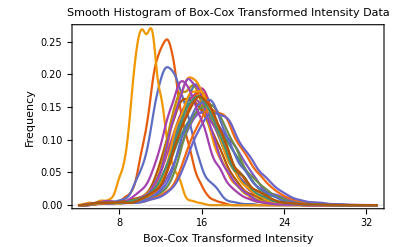

```mathematica
SmoothHistogram[ 
DeleteMissing[#]&/@
boxCoxTransformedMetaboliteData,PlotRange-> All,
PlotTheme->"Scientific",
FrameLabel->{"Box-Cox Transformed Intensity",
"Frequency"},
PlotLabel->
"Smooth Histogram of Box-Cox Transformed Intensity Data"]
```

```mathematica
standardizedMetaboliteData= StandardizeExtended[#,Mean,StandardDeviation]&/@boxCoxTransformedMetaboliteData;
```

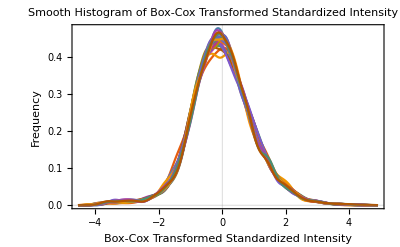

```mathematica
SmoothHistogram[ 
DeleteMissing[#]&/@standardizedMetaboliteData,
PlotRange-> All,PlotTheme->"Scientific",
FrameLabel->
{"Box-Cox Transformed Standardized Intensity",
"Frequency"},
PlotLabel->
"Smooth Histogram of Box-Cox Transformed Standardized Intensity Data"]
```

## Principal Component Analysis

```mathematica
principalComponentsMetabolites=PrincipalComponents[standardizedMetaboliteData/._Missing-> 0,Method->"Correlation"];
```

```mathematica
Dimensions[principalComponentsMetabolites]
```

{21,3247}

```mathematica
varianceRatios=Variance[principalComponentsMetabolites]/Plus@@Variance[principalComponentsMetabolites];
```

```mathematica
varianceRatios[[1;;5]]
```

{0.374437,0.26746,0.097374,0.0624436,0.0412076}

```mathematica
positionsGFAnnotations=Thread[{Range[Length[metabolitesGFAnnotations]],metabolitesGFAnnotations}]
```

{{1,GF},{2,GF},{3,GF},{4,5},{5,5},{6,5},{7,5},{8,10},{9,10},{10,10},{11,10},{12,15},{13,15},{14,15},{15,15},{16,20},{17,20},{18,20},{19,25},{20,25},{21,25}}

```mathematica
groupsGFAnnotations=GroupBy[positionsGFAnnotations,Last-> First]
```

<|GF→{1,2,3},5→{4,5,6,7},10→{8,9,10,11},15→{12,13,14,15},20→{16,17,18},25→{19,20,21}|>

```mathematica
ListPointPlot3D[
principalComponentsMetabolites[[All,
{1,2,3}]][[#]]&/@
(Values@groupsGFAnnotations),
PlotStyle->({#,PointSize[0.025]}&/@#),
PlotLegends-> 
SwatchLegend[#,
Style[#,FontFamily->"Arial"]&/@{"GF","5 Days","10 Days","15 Days","20 Days","25 Days"},
LegendLabel->Style["Mouse Groups",Italic,
FontFamily->"Arial"],
LegendMarkers->"Bubble"],
PlotLabel->
Style[
"Principal Component Analysis of Normalized Feature Data",
Bold,FontFamily->"Arial"],
AxesLabel-> {"P1","P2","P3"}]&@
{Green,Blue,Cyan,Red,Orange,Purple}
```

-Graphics3D-

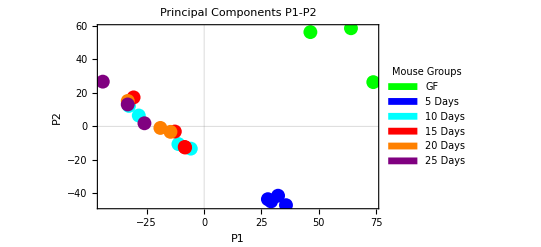

```mathematica
ListPlot[
principalComponentsMetabolites[[All,
{1,2}]][[#]]&/@
(Values@groupsGFAnnotations),
PlotStyle->({#,PointSize[0.025]}&/@#),
PlotLegends-> 
SwatchLegend[#,
Style[#,FontFamily->"Arial"]&/@
{"GF","5 Days","10 Days","15 Days",
"20 Days","25 Days"},
LegendLabel->Style["Mouse Groups",Italic,
FontFamily->"Arial"],
LegendMarkers->"Bubble"],
PlotLabel->Style["Principal Components P1-P2",
Bold,FontFamily->"Arial"],
FrameLabel-> {"P1","P2"},
PlotRange->All,
PlotTheme->"Scientific"]&@
{Green,Blue,Cyan,Red,Orange,Purple}
```

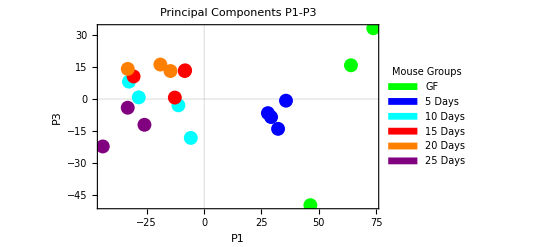

```mathematica
ListPlot[
principalComponentsMetabolites[[All,
{1,3}]][[#]]&/@
(Values@groupsGFAnnotations),
PlotStyle->({#,PointSize[0.025]}&/@#),
PlotLegends-> 
SwatchLegend[#,
Style[#,FontFamily->"Arial"]&/@
{"GF","5 Days","10 Days","15 Days",
"20 Days","25 Days"},
LegendLabel->Style["Mouse Groups",Italic,
FontFamily->"Arial"],
LegendMarkers->"Bubble"],
PlotLabel->Style["Principal Components P1-P3",
Bold,FontFamily->"Arial"],
FrameLabel-> {"P1","P3"},
PlotRange->All,
PlotTheme->"Scientific"]&@
{Green,Blue,Cyan,Red,Orange,Purple}
```

## Differential Analysis GF vs 5 Days After Inoculation

```mathematica
gfD5Micedata=AssociationThread[metabolitesGFFeatures,{#[[1;;3]],#[[4;;7]]}&/@Transpose @standardizedMetaboliteData];
```

```mathematica
gfD5Micedata[[1;;3]]
```

<|269.125→{{1.59827,1.3155,1.9353},{1.20028,1.23387,1.18128,1.10904}},225.083→{{0.513168,0.734814,1.04897},{0.626587,0.702056,0.671343,0.689867}},323.134→{{0.320948,0.200707,0.51853},{0.275585,0.254827,0.257726,0.419021}}|>

```mathematica
Length[gfD5Micedata]
```

3247

```mathematica
Query[All,All,DeleteMissing]@gfD5Micedata;
```

```mathematica
filteredGFd5Data=Query[Select[ (Length[#[[1]]]==3)&&Length[#[[2]]]≥  3&]]@(Query[All,All,DeleteMissing]@gfD5Micedata);
```

```mathematica
Length[filteredGFd5Data]
```

3175

```mathematica
LocationTest[filteredGFd5Data[[1]],Automatic,{"TestDataTable",All}]
```

| Statistic | P-Value
Mann-Whitney | 12. | 0.0215563
T | 2.40355 | 0.132893
Z | 2.40355 | 0.0162366

```mathematica
LocationTest[filteredGFd5Data[[1]],Automatic,"TestConclusion"]
```

The null hypothesis that the mean difference is 0 is not rejected at the 5 percent level based on the T test.

```mathematica
testGFd5Conclusions=Query[All,LocationTest[#,Automatic,{"PValue","ShortTestConclusion"}]&]@filteredGFd5Data;
```

```mathematica
testGFd5Conclusions[[1;;3]]
```

<|269.125→{0.132893,Do not reject},225.083→{0.610388,Do not reject},323.134→{0.640274,Do not reject}|>

```mathematica
Length[#]&/@GroupBy[testGFd5Conclusions,Last]
```

<|Do not reject→1724,Reject→1451|>

```mathematica
testGFd5ConclusionsBFCorrected=Query[All,LocationTest[#,Automatic,{"PValue","ShortTestConclusion"},SignificanceLevel->(0.05/3175)]&]@filteredGFd5Data;
```

```mathematica
Length[#]&/@GroupBy[testGFd5ConclusionsBFCorrected,Last]
```

<|Do not reject→3088,Reject→87|>

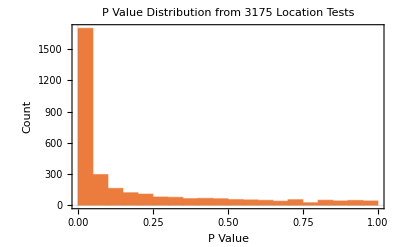

```mathematica
Histogram[testGFd5ConclusionsBFCorrected[[All,1]],
PlotTheme->"Scientific",
PlotLabel->
"P Value Distribution from 3175 Location Tests",
FrameLabel-> {"P Value", "Count"}]
```

```mathematica
testGFd5FDRResults=BenjaminiHochbergFDR[Values@testGFd5ConclusionsBFCorrected[[All,1]],SignificanceLevel-> 0.05];
```

```mathematica
d
```

d

```mathematica
Query["Results",1;;5]@testGFd5FDRResults
```

{{0.0361271,0.0723224,False},{0.510254,0.59083,False},{0.640274,0.70732,False},{0.00260507,0.0106799,True},{0.137148,0.204915,False}}

```mathematica
testGFd5FDRResults["p-Value Cutoff"]
```

0.0217436

```mathematica
testGFd5FDRResults["q-Value Cutoff"]
```

0.0497377

```mathematica
pValuesGFd5FDR=Query["Results",(AssociationThread[Keys[testGFd5ConclusionsBFCorrected]-> #]&)]@testGFd5FDRResults;
pValuesGFd5FDR//Short[#,4]&
```

<|269.125→{0.0361271,0.0723224,False},«3173»,235.178→{0.418964,0.505976,False}|>

```mathematica
significantQuery=Query[Select[#[[3]]==True&]]@pValuesGFd5FDR;
```

```mathematica
significantQuery[[1;;3]]
```

<|86.0247→{0.00260507,0.0106799,True},301.056→{0.00411965,0.0145214,True},130.039→{0.000253831,0.00220311,True}|>

```mathematica
Length[significantQuery]
```

1388

```mathematica
deltaGFd5Data=Query[All,Mean[#[[2]]]-Mean[#[[1]]]&]@filteredGFd5Data;
```

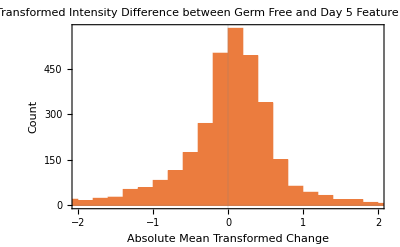

```mathematica
Histogram[deltaGFd5Data,
PlotTheme->"Scientific",
PlotLabel->
"Transformed Intensity Difference between
 Germ Free and Day 5 Feature Intensities",
FrameLabel->{"Absolute Mean Transformed Change",
"Count"}]
```

```mathematica
pValueNegLogGFd5Data= -Log10@Query[All,2]@pValuesGFd5FDR;
```

```mathematica
volcanoPlotGFd5Data=Merge[{deltaGFd5Data,pValueNegLogGFd5Data},Identity];
```

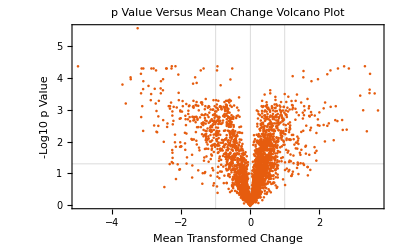

```mathematica
ListPlot[Values@volcanoPlotGFd5Data,
PlotTheme-> "Scientific",
PlotRange-> Full,
PlotLabel-> 
"p Value Versus Mean Change Volcano Plot",
FrameLabel->{"Mean Transformed Change", "-Log10 p Value"},
GridLines->
{{{-1,{Red,Thick,Dashed}},0,
{1,{Red,Thick,Dashed}}},
{{-Log10[0.05],{Blue,Thick,Dashed}}}}]
```

```mathematica
selectedFeaturesGFd5=Query[Select[Abs[#[[1]]]>1&& #[[2]]> (-Log10[0.05])&]]@volcanoPlotGFd5Data;
```

```mathematica
Length[selectedFeaturesGFd5]
```

366

```mathematica
selectedFeaturesGFd5[[1;;10]]
```

<|238.045→{-1.65905,3.09779},338.146→{2.71869,4.37504},388.136→{-2.3985,2.57451},279.038→{-1.88966,1.9473},128.028→{-1.35472,2.17012},178.983→{-1.43019,2.45974},420.109→{-2.2604,1.73732},128.034→{-1.3964,2.23483},353.085→{-2.00294,1.85289},178.034→{-1.21014,2.1053}|>

## Identifying Compounds Using ChemSpider

```mathematica
chemSpider=ServiceConnect["ChemSpider"]
```

ServiceObject[…]

```mathematica
chemSpiderDatabases=chemSpider["Databases"];
```

```mathematica
chemSpiderDatabases[[1;;10]]
```

{4C Pharma Scientific,A&A Life Science,A1 BioChem Labs,A2Z Chemical,Abblis Chemicals,Abcam,abcr,ACB Blocks,Accel Pharmtech,Accela ChemBio}

```mathematica
chemSpiderDatabases//Short
```

{4C Pharma Scientific,«575»,Zylexa Pharma}

```mathematica
SystemOpen["paclet:ref/service/ChemSpider"]
```

```mathematica
idExample=chemSpider["Search",
"Mass"-> 238.0452933,"Range"->0.001,MaxItems->5]
```

Dataset[<>]

```mathematica
Normal@idExample
```

{<|ID→63109|>,<|ID→71899|>,<|ID→81385|>,<|ID→90104|>,<|ID→91088|>}

```mathematica
id63109Info=chemSpider["CompoundInformation",
"ID"->"63109"]
```

Dataset[<>]

```mathematica
Head[id63109Info]
```

Dataset

```mathematica
Normal@id63109Info
```

<|CSID→63109,InChI→InChI=1S/C15H10OS/c16-13-10-15(11-6-2-1-3-7-11)17-14-9-5-4-8-12(13)14/h1-10H,InChIKey→GIQPSSZMIZARDW-UHFFFAOYSA-N,SMILES→c1ccc(cc1)c2cc(=O)c3ccccc3s2|>

```mathematica
extended63109Info=
chemSpider["ExtendedCompoundInformation",
"ID"-> "63109"]
```

Dataset[<>]

```mathematica
chemSpider["CompoundThumbnail","ID"-> "63109"]
```

-Graphics-

```mathematica
Normal@chemSpider["Search","Query"->"2-Phenyl-4H-thiochromen-4-one"]
```

<|ID→63109|>

```mathematica
resultsIDs=chemSpider["Search","Mass"-> #,"Range"->(5*10^(-6)*#),MaxItems->5]&/@(Keys@selectedFeaturesGFd5);
```

```mathematica
Tally[Length[#]&/@resultsIDs]
```

{{5,308},{1,37},{0,21}}

```mathematica
positionsChemSpiderUnique=Position[resultsIDs,x_/;Length[x]==1]
```

{{5},{14},{15},{17},{38},{42},{44},{46},{49},{56},{58},{66},{67},{83},{85},{111},{113},{131},{174},{175},{192},{202},{211},{216},{217},{221},{231},{234},{262},{263},{284},{286},{292},{296},{300},{359},{361}}

```mathematica
chemSpiderUniqueIDs=Query[(Select[Length[#]==1&]),1]@resultsIDs
```

{10695492,57522026,8117740,16127232,4484268,10816284,183101,120057,9963870,2062433,2849023,183101,10531457,8139662,455565,57532061,9052908,4890256,57269218,2050613,364974,1544479,9193986,376658,5496216,10816284,1544479,2796974,9228003,49071248,23136140,71333,109782,559241,9732048,9140563,1554167}

```mathematica
featuresGFd5ChemSpiderID=AssociationThread[Extract[Keys@selectedFeaturesGFd5,positionsChemSpiderUnique],chemSpiderUniqueIDs]
```

<|128.028→10695492,147.011→57522026,99.0075→8117740,150.989→16127232,87.0074→4484268,92.9827→10816284,94.9783→183101,106.998→120057,86.0234→9963870,176.001→2062433,96.0442→2849023,94.9784→183101,84.0442→10531457,92.0573→8139662,91.054→455565,74.0234→57532061,173.1→9052908,132.048→4890256,198.91→57269218,195.913→2050613,89.1077→364974,134.027→1544479,82.0155→9193986,193.162→376658,192.159→5496216,92.9831→10816284,134.027→1544479,130.032→2796974,207.115→9228003,107.049→49071248,170.98→23136140,167.926→71333,71.0861→109782,99.0807→559241,76.0398→9732048,191.12→9140563,176.094→1554167|>

```mathematica
featuresGFd5ChemSpiderIDExtended=Query[All,Normal@chemSpider["ExtendedCompoundInformation","ID"->#]&]@featuresGFd5ChemSpiderID;
```

```mathematica
Query[1,Keys]@featuresGFd5ChemSpiderIDExtended
```

{CSID,MF,SMILES,InChI,InChIKey,AverageMass,MolecularWeight,MonoisotopicMass,NominalMass,ALogP,XLogP,CommonName}

```mathematica
Query[All,"CommonName"]@featuresGFd5ChemSpiderIDExtended
```

<|128.028→2-Furyl dihydrogen borate,147.011→2,4,6,8,10-Undecapentaynenitrile,99.0075→Beryllium diformate,150.989→3-Mercapto-2-mercaptomethylpropanoate,87.0074→(2R)-2-Hydroxy-4-oxo-1-oxoniabicyclo[1.1.0]butane,92.9827→SODIUM NITRILOACETATE,94.9783→Phosphoramidate,106.998→Acrylonitrile, trifluoro-,86.0234→Hydroxy(2-oxopropylidyne)ammonium,176.001→3-(Chloromethyl)-1,1,2,2-tetrafluorocyclobutane,96.0442→3-Pyridinyloxonium,94.9784→Phosphoramidate,84.0442→3-Methyl-1,3-oxazol-3-ium,92.0573→DL-Alanine-13C3,91.054→Phenylmethylium,74.0234→4,5-Dihydro-1,3,2-dioxazol-1-ium,173.1→Cyclohexyl(dimethoxy)silyl,132.048→1-Oxo-2-sulfanylpiperidinium,198.91→1-Butene, zinc salt, hydrobromide (1:1:1),195.913→2,2,2-Trichloroethanimidamide hydrochloride (1:1),89.1077→1-Ethyl-1,1-dimethylhydrazinium,134.027→2,5-Dihydro-3-thiophenaminium 1,1-dioxide,82.0155→2-Chloro(1,1-~2~H_2_)ethanol,193.162→1,2-Ethanediamine - 2-(butylsulfanyl)ethanamine (1:1),192.159→(2S)-2-Hydroxy-N,N-bis[(2R)-2-hydroxypropyl]-1-propanaminium,92.9831→SODIUM NITRILOACETATE,134.027→2,5-Dihydro-3-thiophenaminium 1,1-dioxide,130.032→3-(2-Hydroxyethyl)-1,3-thiazol-3-ium,207.115→Butyl(diethoxymethyl)oxophosphonium,107.049→L-(1,2-~13~C_2_)Serine,170.98→3-Amino-1-propaneseleninic acid,167.926→TRIFLUOROMETHANESULFONYLCHLORIDE,71.0861→Pentyl,99.0807→1-Oxohex-1-ylium,76.0398→Ethyl (~14~C)formate,191.12→Methoxy(octyl)oxophosphonium,176.094→7-Chloro-1,3,5-triazoniatricyclo[3.3.1.1~3,7~]decane|>

```mathematica
Query[All,"CSID"]@featuresGFd5ChemSpiderIDExtended
```

<|128.028→10695492,147.011→57522026,99.0075→8117740,150.989→16127232,87.0074→4484268,92.9827→10816284,94.9783→183101,106.998→120057,86.0234→9963870,176.001→2062433,96.0442→2849023,94.9784→183101,84.0442→10531457,92.0573→8139662,91.054→455565,74.0234→57532061,173.1→9052908,132.048→4890256,198.91→57269218,195.913→2050613,89.1077→364974,134.027→1544479,82.0155→9193986,193.162→376658,192.159→5496216,92.9831→10816284,134.027→1544479,130.032→2796974,207.115→9228003,107.049→49071248,170.98→23136140,167.926→71333,71.0861→109782,99.0807→559241,76.0398→9732048,191.12→9140563,176.094→1554167|>

```mathematica
Query[{7},"SMILES"]@featuresGFd5ChemSpiderIDExtended
```

<|94.9783→NP(=O)([O-])[O-]|>

```mathematica
chemSpiderIDMOL=Query[1;;3,"CSID",Normal@chemSpider["GetIdentifier",{"Identifier"-> "MOL","ID"->ToExpression[#]}]&]@featuresGFd5ChemSpiderIDExtended;
```

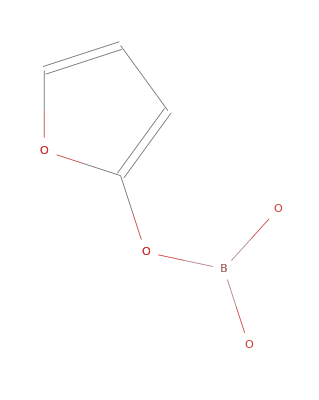
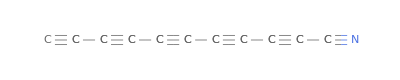
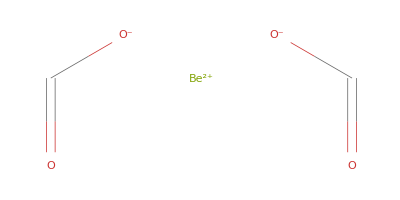
<|128.028→-Graphics-,147.011→-Graphics-,99.0075→-Graphics-|>

```mathematica
Query[All,1,ImportString[#,"MOL"]&]@
chemSpiderIDMOL
```

```mathematica
ServiceDisconnect[chemSpider]
```

## Identifying Compounds and Pathway Analysis: KEGG

```mathematica
putativeIDs=MassMatcher[#,3]&/@Keys@selectedFeaturesGFd5;
```

```mathematica
putativeIDs//Short
```

{{},{},«362»,{},{}}

```mathematica
Tally[putativeIDs]
```

{{{},346},{{cpd:C01852,cpd:C09781,cpd:C09802},1},{{cpd:C18409},1},{{cpd:C16698,cpd:C19770,cpd:C21027},1},{{cpd:C18922},1},{{cpd:C08503,cpd:C14538},1},{{cpd:C05983},1},{{cpd:C09123},1},{{cpd:C18421},1},{{cpd:C14648},1},{{cpd:C18553},1},{{cpd:C06862},1},{{cpd:C17132,cpd:C17133,cpd:C17136},1},{{cpd:C05366,cpd:C08831,cpd:C09077,cpd:C09515,cpd:C09516,cpd:C10317,cpd:C10558,cpd:C10682,cpd:C17414,cpd:C17508,cpd:C17808,cpd:C20455},1},{{cpd:C00062,cpd:C00792,cpd:C02385},1},{{cpd:C10545,cpd:C10563,cpd:C10640},1},{{cpd:C09098},1},{{cpd:C17704},1},{{cpd:C15193,cpd:C18927},1},{{cpd:C17364},1},{{cpd:C15660},1}}

```mathematica
ppm10putativeIDs=MassMatcher[#,10]&/@Keys@selectedFeaturesGFd5;
```

```mathematica
ppm10putativeIDs[[1;;45]]
```

{{},{cpd:C19333},{cpd:C01852,cpd:C04541,cpd:C09781,cpd:C09802},{},{cpd:C16472,cpd:C16473},{},{},{cpd:C08734},{cpd:C18592},{},{},{},{},{},{},{},{},{},{},{},{},{cpd:C08477,cpd:C10583},{},{},{},{},{cpd:C20313},{},{cpd:C08549},{},{},{},{},{},{},{cpd:C18409},{},{},{},{},{},{},{},{},{}}

```mathematica
positionsPutativeIDs=Position[putativeIDs,x_/;Length[x]==1]
```

{{36},{75},{161},{181},{186},{187},{206},{230},{314},{346},{360},{364}}

```mathematica
selectedFeaturesGFd5[[{360}]]
```

<|315.144→{1.91576,2.275}|>

```mathematica
accessionPutativeIDs=Flatten@Extract[putativeIDs,positionsPutativeIDs]
```

{cpd:C18409,cpd:C18922,cpd:C05983,cpd:C09123,cpd:C18421,cpd:C14648,cpd:C18553,cpd:C06862,cpd:C09098,cpd:C17704,cpd:C17364,cpd:C15660}

```mathematica
compoundDictionary=KEGGDictionary[KEGGQuery1-> "cpd",KEGGQuery2-> ""];
```

```mathematica
compoundDictionary[[1;;10]]
```

<|cpd:C00001→H2O; Water,cpd:C00002→ATP; Adenosine 5'-triphosphate,cpd:C00003→NAD+; NAD; Nicotinamide adenine dinucleotide; DPN; Diphosphopyridine nucleotide; Nadide; beta-NAD+,cpd:C00004→NADH; DPNH; Reduced nicotinamide adenine dinucleotide,cpd:C00005→NADPH; TPNH; Reduced nicotinamide adenine dinucleotide phosphate,cpd:C00006→NADP+; NADP; Nicotinamide adenine dinucleotide phosphate; beta-Nicotinamide adenine dinucleotide phosphate; TPN; Triphosphopyridine nucleotide; beta-NADP+,cpd:C00007→Oxygen; O2,cpd:C00008→ADP; Adenosine 5'-diphosphate,cpd:C00009→Orthophosphate; Phosphate; Phosphoric acid; Orthophosphoric acid,cpd:C00010→CoA; Coenzyme A; CoA-SH|>

```mathematica
Query[accessionPutativeIDs]@compoundDictionary
```

<|cpd:C18409→Cycloprothrin,cpd:C18922→Dinocton 6,cpd:C05983→Propionyladenylate; Propionyl-adenosine monophosphate,cpd:C09123→Athamantin,cpd:C18421→Propamocarb hydrochloride,cpd:C14648→6alpha-Chloro-17-acetoxyprogesterone; 6alpha-Chloro-17-hydroxypregn-4-ene-3,20-dione acetate,cpd:C18553→Spirodiclofen,cpd:C06862→Busulfan,cpd:C09098→Canthin-6-one; 6H-Indolo(3,2,1-de)(1,5)naphthyridin-6-one,cpd:C17704→Antibiotic JI-20A; JI-20A,cpd:C17364→Clavamycin D,cpd:C15660→A 77003|>

```mathematica
Entity["Chemical","Busulfan"]
```

busulfan

```mathematica
Entity["Chemical","Busulfan"]
```

busulfan

```mathematica
CanonicalName[#]&/@Entity["Chemical"]["Properties"]
```

{AcidityConstants,AdjacencyMatrix,AlternateNames,AtomPositions,AutoignitionPoint,BeilsteinNumber,BlackStructureDiagram,BoilingPoint,BondCounts,BondEnergies,BondLengths,CASNumber,CHBlackStructureDiagram,CHColorStructureDiagram,CIDNumber,Codons,ColorStructureDiagram,CombustionHeat,CriticalPressure,CriticalTemperature,Density,DielectricConstant,DipoleMoment,DOTHazardClass,DOTNumbers,EdgeRules,EdgeTypes,EGECNumber,ElectronAffinity,ElementCounts,ElementMassFraction,ElementTypes,EUNumber,FlashPoint,FormalCharges,FormattedName,Formula,FormulaString,FusionHeat,GmelinNumber,HBondAcceptorCount,HBondDonorCount,HenryLawConstant,HildebrandSolubility,HillFormula,HillFormulaString,InChI,IonCounts,IonEquivalents,Ions,IsoelectricPoint,IsomericSMILES,Isomers,IUPACName,LewisDotStructureDiagram,LightSpeed,LogAcidityConstants,LowerExplosiveLimit,MDLNumber,MeanFreePath,MeltingPoint,Memberships,MolarMass,MolarVolume,MolecularMass,MoleculePlot,MultiBondMoleculePlot,MultiBondStickMoleculePlot,Name,NetCharge,NFPAFireRating,NFPAHazards,NFPAHealthRating,NFPALabel,NFPAReactivityRating,NonHydrogenCount,NonStandardIsotopeCount,NonStandardIsotopeCounts,NonStandardIsotopeNumbers,NSCNumber,OdorThreshold,OdorType,PartitionCoefficient,pH,Phase,ProtonAffinity,RefractiveIndex,RelativeMolecularMass,Resistivity,RotatableBondCount,RTECSClasses,RTECSNumber,SideChainLogAcidityConstant,SMILES,Solubility,SpaceFillingMoleculePlot,StandardName,StickMoleculePlot,SurfaceTension,TautomerCount,ThermalConductivity,TopologicalPolarSurfaceArea,UpperExplosiveLimit,VanDerWaalsConstants,VaporDensity,VaporizationHeat,VaporPressure,VertexCoordinates,VertexTypes,Viscosity}

```mathematica
Entity["Chemical","Busulfan"][{"CASNumber","CIDNumber","Formula","IUPACName","MolarMass","MolecularMass"}]
```

{CAS55-98-1,CID2478,CH_3SO_2O(CH_2)_4OSO_2CH_3,methanesulfonic acid 4-methylsulfonyloxybutyl ester,246.3 g/mol,246.3 u}

```mathematica
Entity["Chemical","Busulfan"]["StickMoleculePlot"]
```

-Graphics3D-

NADH

WolframAlphaQueryResults

```mathematica
KEGGAnalysis[accessionPutativeIDs,FilterSignificant-> False,AnalysisType-> "Molecular"]
```

<|path:map07218→{{0.00256629,0.0102652,True},{3,5,5841,1},{HIV protease inhibitors,{{cpd:C15660}}}},path:map00640→{{0.0244554,0.0489109,True},{3,48,5841,1},{Propanoate metabolism,{{cpd:C05983}}}},path:map00524→{{0.0410351,0.0547135,False},{3,81,5841,1},{Neomycin, kanamycin and gentamicin biosynthesis,{{cpd:C17704}}}},path:map01130→{{0.369022,0.369022,False},{3,831,5841,1},{Biosynthesis of antibiotics,{{cpd:C17704}}}}|>

```mathematica
ppm10positionsPutativeIDs=Position[ppm10putativeIDs,x_/;Length[x]==1];
```

```mathematica
ppm10accessionPutativeIDs=Flatten@Extract[ppm10putativeIDs,ppm10positionsPutativeIDs];
```

```mathematica
ppm10accessionPutativeIDs//Short
```

{cpd:C19333,cpd:C08734,«47»,cpd:C08264,cpd:C17364}

```mathematica
keggPathways10ppm=KEGGAnalysis[ppm10accessionPutativeIDs,FilterSignificant-> False,AnalysisType-> "Molecular"];
```

```mathematica
Length[%]
```

15

```mathematica
keggPathways10ppm[[1;;3]]
```

<|path:map00791→{{0.000795184,0.0119278,True},{12,21,5841,2},{Atrazine degradation,{{cpd:C08734},{cpd:C06553}}}},path:map00331→{{0.0203711,0.152783,False},{12,10,5841,1},{Clavulanic acid biosynthesis,{{cpd:C06656}}}},path:map00450→{{0.0541309,0.174115,False},{12,27,5841,1},{Selenocompound metabolism,{{cpd:C05690}}}}|>

```mathematica
KEGGPathwayVisual["path:map00791"]
```

<|Pathway→path:map00791,Results→{http://www.kegg.jp/kegg-bin/show_pathway?map=map00791}|>